```mathematica
x = x[t];
θ = θ[t];
v = x'[t];
wt = θ'[t];

u = u[t];

CM0= {x, 0};
CM1= CM0 +{l1cm*Sin[θ],l1cm*Cos[θ]};

V0 = D[CM0, t];
V1 = D[CM1, t];

T= 1/2 * (M * V0.V0 + m1 * V1.V1 ) + 1/2 * (I1*wt*wt );
V= g*(m1*CM1[[2]]);

L =T- V;

eq1 = (D[D[L,  v ], t] - D[L, x] == u) //Simplify;
eq2 = (D[D[L, wt], t] - D[L, θ] == -η1*wt)//Simplify;

motionEquations = Solve[eq1 && eq2 , {x''[t], θ''[t]}][[1]] //Simplify;
```

```mathematica
motionEquations // TraditionalForm
L // TraditionalForm
```

{x''(t)→(l1cm m1 ((θ'(t))^2 (I1+l1cm^2 m1) sin(θ[t])+η1 θ'(t) cos(θ[t])-g l1cm m1 sin(θ[t]) cos(θ[t]))+u(t) (I1+l1cm^2 m1))/((M+m1) (I1+l1cm^2 m1)-l1cm^2 m1^2 cos^2(θ[t])),θ''(t)→-((2 (l1cm^2 m1^2 (θ'(t))^2 sin(θ[t]) cos(θ[t])-g l1cm m1 (M+m1) sin(θ[t])+l1cm m1 u(t) cos(θ[t])+η1 (M+m1) θ'(t)))/(-l1cm^2 m1^2 cos(2 θ[t])+2 I1 (M+m1)+l1cm^2 m1 (2 M+m1)))}

-g l1cm m1 cos(θ[t])+1/2 (m1 (l1cm^2 (θ'(t))^2 sin^2(θ[t])+(l1cm θ'(t) cos(θ[t])+x'(t))^2)+M (x'(t))^2)+1/2 I1 (θ'(t))^2

```mathematica
params = {
	g ->9.8,
l1->.15,
	l1cm -> .075,
m1 -> .15,
	M -> .32,
	I1->m1*l1^2/12,
	η1->0
};
```

```mathematica
ssm = StateSpaceModel[
	{eq1, eq2},
	{
		{x, 0},
		{v, 0},
		{θ, 0},
		{wt, 0}
	},
	{u},
	{x, θ},
	t
]  //Simplify

A = ssm[[1, 1]] //. params;
B = ssm[[1, 2]] //. params;

A //MatrixForm
B // MatrixForm
```

0100000-(g l1cm^2 m1^2)/(l1cm^2 M m1+I1 (M+m1))(l1cm m1 η1)/(l1cm^2 M m1+I1 (M+m1))(I1+l1cm^2 m1)/(l1cm^2 M m1+I1 (M+m1))0001000(g l1cm m1 (M+m1))/(l1cm^2 M m1+I1 (M+m1))-((M+m1) η1)/(l1cm^2 M m1+I1 (M+m1))-(l1cm m1)/(l1cm^2 M m1+I1 (M+m1))1000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x[t],0},x_1,{θ[t],0},x_2},{{u[t],0}},Automatic,t

(0 | 1 | 0 | 0
0 | 0 | -3.08392 | 0.
0 | 0 | 0 | 1
0 | 0 | 128.839 | 0.)

(0
2.7972
0
-27.972)

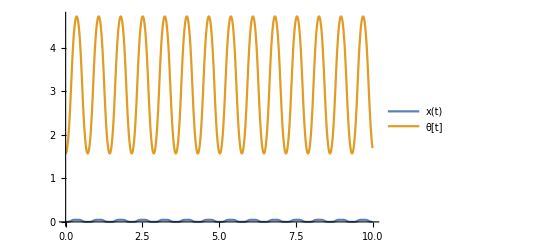

```mathematica
(*Simulation without control*)
T=10;

initialConditions = {
x == v == wt==0,
θ == .5Pi
} /. t-> 0;

eqnsNonLinear = Flatten[{
	eq1, eq2,
	initialConditions
}] //. params /. u->0 /. {x->a, θ->b}; 

solsN = NDSolve[eqnsNonLinear, { a, b}, {t, T}][[1]];
Plot[Evaluate[{a[t], b[t]} /.  solsN], {t, 0, T},PlotLegends->{x, θ}]
```

```mathematica
(*Simulation with continuous control*)
```

```mathematica
Qmatrix = DiagonalMatrix[{100, .001, .1, .0001}];
Rmatrix = DiagonalMatrix[{.5}];
Klqr = LQRegulatorGains[ssm //. params, {Qmatrix, Rmatrix}];

initialConditionsCTRB ={
x == v == 0,
θ == wt == .3
} /. t->0;
T = 4;

setpoint = {0, 0, 0, 0};
s = {x, v, θ, wt};
controlLQR = {u -> -Klqr.(s-setpoint)};

eqnsControlLQR = Flatten[{
	eq1, eq2,
	initialConditionsCTRB
}] //. params /. controlLQR /.{x->a, θ->b};

solsNLQR=NDSolve[eqnsControlLQR,{a, b},{t,0,T}];
```

```mathematica
Klqr // TraditionalForm
```

(-14.1421 | -6.25903 | -18.1789 | -1.72084)

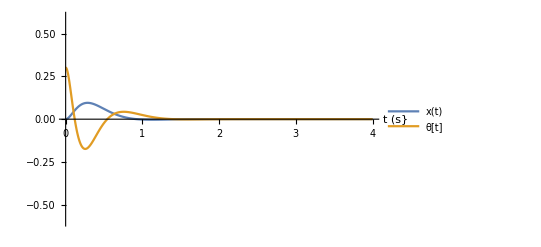

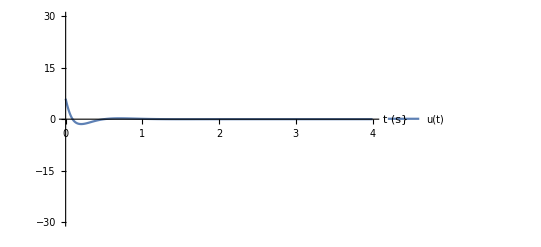

```mathematica
Plot[
	Evaluate[{a[t],b[t]}/.  solsNLQR],
	{t,0,T},
	PlotLegends->{x, θ, u},
	PlotRange->{-.6,.6},
	AxesLabel->{"t (s}"}
]
Plot[
	Evaluate[u/. controlLQR/. {x->a,θ->b}/.  solsNLQR],
	{t,0,T},
	PlotLegends->{u},
	PlotRange->{-30,30},
	AxesLabel->{"t (s}"}
]
```

```mathematica
(*Controllo impulsivo*)
τ = .005;
Qmatrix = DiagonalMatrix[{1, .1, 10, 1}];
Rmatrix = DiagonalMatrix[{.5}];

ssmd = ToDiscreteTimeModel[ssm //. params, τ];

Klqrd=DiscreteLQRegulatorGains[ssm //. params, {Qmatrix, Rmatrix}, τ];
(*Klqrd = StateFeedbackGains[ssmd, {.1, .2, .3, .4, .5, .6}]*)

Ad = ssmd[[1, 1]];
Bd = ssmd[[1, 2]];
Klqrd // TraditionalForm
```

(-1.25549 | -1.578 | -13.7093 | -1.74257)

```mathematica
initialConditionsCTRBd = {0, 0,.1, -.1};

solutions = {};
steps = {initialConditionsCTRBd};
uSteps = {};

T = 5;
For[k=0,k< T/τ,++k,
	eqnsControlLQR = Flatten[{
		eq1, eq2,
		steps[[-1]]  == {x, v, θ, wt}/. {t->k*τ}
	}] //. params /.{x->a, θ->b, u-> (-Klqrd.(steps[[-1]]))[[1]]};

	AppendTo[solutions, NDSolve[eqnsControlLQR,{a,b},{t,k*τ,(k+1)τ}][[1]]];
	f = solutions[[-1]];
	step = {f[[1, 2]][t], f[[1, 2]]'[t], f[[2, 2]][t], f[[2, 2]]'[t]} /. t-> (k+1)τ; 

	AppendTo[steps, step];
	AppendTo[uSteps, (-Klqrd.(steps[[-1]]))[[1]]];
]
```

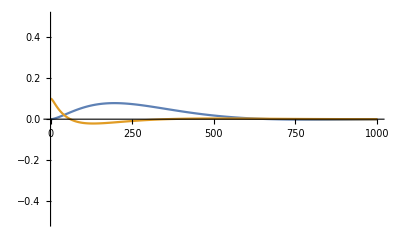

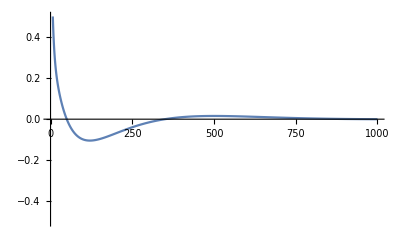

```mathematica
points = steps  //Transpose;
toPlot = {points[[1]], points[[3]]};
ListPlot[toPlot, {Joined->True, PlotRange->{-0.5, .5}}]
ListPlot[uSteps,{Joined->True, PlotRange->{-0.5, .5}}]
```

{u[t]→5.5 Tanh[Cos[θ[t]] θ'[t] (0.11025 (-1+Cos[θ[t]])+0.0005625 θ'[t]^2)]}

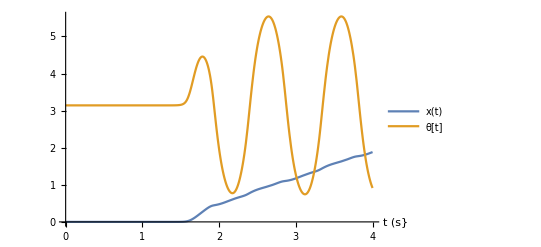

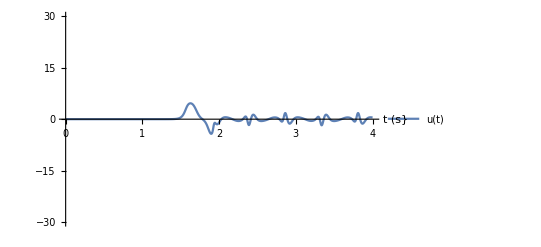

```mathematica
initialConditionsS1={x==v==wt==0,θ==Pi}/. t->0;
T1=4;

setpoint={0,0,0,0};(*Make sure to change setpoint in eqnsControl as well*)
s={x,v,θ,wt};

E1[θ_, wt_]:= 1/2 I1*wt^2 + m1*g*l1cm*(Cos[θ] - 1) + 1/2 m1*(l1cm*wt)^2 (* Todo rewrite pls*)
E11[θ_, wt_] := E1[θ, wt] //. params
ua1 = 5.5;
(*Qui ci andrebbe Sign al posto di Tanh, ma vabbè*)
controlS1={u -> ua1*Tanh[E11[θ, wt]*wt*Cos[θ]]}

eqnsS1=Flatten[{eq1,eq2,initialConditionsS1}]//.params/. controlS1/. {x->a,θ->b};

solsS1=NDSolve[eqnsS1,{a,b},{t,0,T1}];

Plot[Evaluate[{a[t],b[t]}/.  solsS1],{t,0,T1},PlotLegends->{x,θ,u},PlotRange->{2Pi,-1},AxesLabel->{"t (s}"}]
Plot[Evaluate[u/. controlS1/. {x->a,θ->b}/.  solsS1],{t,0,T1},PlotLegends->{u},PlotRange->{-30,30},AxesLabel->{"t (s}"}]
```